“Network Rules for Group Sarah” / UD RC11 - UCL Bartlett 
29 11 2019
Philippe Morel

PART 2/2

1)
In Part 1 we have seen how we can build lists of values to use for graph representations but also for replacement rules.
Here we will see how we can make a more advanced use of your substitution strategy, by assigning geometric data

Let us first reasign a global value for the size of the images:

```mathematica
imageSizeValue=600
```

600

And recall your starting point:

```mathematica
SubstitutionSystem[{"G"->"F   F   F   F   F","F"->"A  E  A  E  A  E  A", "A"->"B B H B B","E"->"D H D"},"G",3]
```

{G,F   F   F   F   F,A  E  A  E  A  E  A   A  E  A  E  A  E  A   A  E  A  E  A  E  A   A  E  A  E  A  E  A   A  E  A  E  A  E  A,B B H B B  D H D  B B H B B  D H D  B B H B B  D H D  B B H B B   B B H B B  D H D  B B H B B  D H D  B B H B B  D H D  B B H B B   B B H B B  D H D  B B H B B  D H D  B B H B B  D H D  B B H B B   B B H B B  D H D  B B H B B  D H D  B B H B B  D H D  B B H B B   B B H B B  D H D  B B H B B  D H D  B B H B B  D H D  B B H B B}

G should be replaced by {f,f,f,f,f}, like this: g→{f,f,f,f,f}
F should be replaced by {a,e,a,e,a,e,a}, like this: f→{a,e,a,e,a,e,a}
A should be replaced by {b,b,h,b,b}, like this: a→{b,b,h,b,b}
E should be replaced by {d,h,d}, like this: e→{d,h,d}

```mathematica
Clear[a,b,c,d,e,f,g,h];
SubstitutionStep0=g;
SubstitutionStep1=g/.g->{f,f,f,f,f}
```

{f,f,f,f,f}

```mathematica
SubstitutionStep2=SubstitutionStep1/.f->{a,e,a,e,a,e,a}
```

{{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a}}

```mathematica
SubstitutionStep3=SubstitutionStep2/.{a->{b,b,h,b,b},e->{d,h,d}}
```

{{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}}}

2)
If you want, you can visualize these steps in a Cellular Automata like representation, making use of pixel based ArrayPlot.
For that, you first need to assemble the data:

```mathematica
SubstitutionStepAll={SubstitutionStep1,SubstitutionStep2,SubstitutionStep3}
```

{{f,f,f,f,f},{{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a}},{{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}}}}

But the data (the sublists) do not have the same lengths, as you can see below.
Parts are missing in the matrix, so this is not a matrix... (we will replace the missing values by zeros to make it become a real matrix)

```mathematica
MatrixForm[SubstitutionStepAll]
```

(f | f | f | f | f
{a,e,a,e,a,e,a} | {a,e,a,e,a,e,a} | {a,e,a,e,a,e,a} | {a,e,a,e,a,e,a} | {a,e,a,e,a,e,a}
{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}} | {{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}} | {{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}} | {{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}} | {{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}})

You can check:

```mathematica
MatrixQ[SubstitutionStepAll]
```

False

You can also see that the matrix has 3 rows and 5 columns (until level 2, beyond that level lists don’t have the same lengths anymore)

```mathematica
SubstitutionStepAll//Dimensions
SubstitutionStepAll//ArrayDepth
```

{3,5}

2

Let’s reformat the repetitive part of SubstitutionStepAll to obtain, for 1 full column (I mean for one F), the successive replacements:

```mathematica
SubstitutionStepRepetitivePart=List/@SubstitutionStepAll[[All,1]];
Flatten/@SubstitutionStepRepetitivePart
```

{{f},{a,e,a,e,a,e,a},{b,b,h,b,b,d,h,d,b,b,h,b,b,d,h,d,b,b,h,b,b,d,h,d,b,b,h,b,b}}

```mathematica
SubstitutionStepRepetitivePartOK=CenterArray[%,All]/.{a->1,b->2,c->3,d->4,e->5,f->6,g->7,h->8}
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,5,1,5,1,5,1,0,0,0,0,0,0,0,0,0,0,0},{2,2,8,2,2,4,8,4,2,2,8,2,2,4,8,4,2,2,8,2,2,4,8,4,2,2,8,2,2}}

```mathematica
SubstitutionStepRepetitivePartOK//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 5 | 1 | 5 | 1 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 8 | 2 | 2 | 4 | 8 | 4 | 2 | 2 | 8 | 2 | 2 | 4 | 8 | 4 | 2 | 2 | 8 | 2 | 2 | 4 | 8 | 4 | 2 | 2 | 8 | 2 | 2)

Let’s print the repetitive part (with element F at the top, here replaced by number 6)

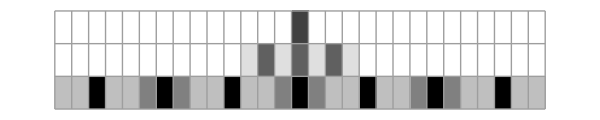

```mathematica
ArrayPlot[SubstitutionStepRepetitivePartOK,Mesh->All,ImageSize->imageSizeValue]
```

All everything (without the G for the moment)

```mathematica
SubstitutionStepAlmostOK=Flatten/@Transpose[Table[SubstitutionStepRepetitivePartOK,5]];
ArrayPlot[%,AspectRatio->Automatic,Mesh->All,ImageSize->imageSizeValue]
```

-Graphics-

Let’s add the G (it means adding one row at the beginning, with central value being 7):

```mathematica
SubstitutionStepOK=Prepend[SubstitutionStepAlmostOK,CenterArray[7,145]];
```

```mathematica
ArrayPlot[SubstitutionStepOK,AspectRatio->Automatic,Mesh->All,ImageSize->imageSizeValue]
```

-Graphics-

3)
This representation is more or less ok but it is far from perfect. In fact the relationships between the cells aren’t clear, since I replace one cell by multiple other cells...
So it would better to start with a G as a unit square (you’ll be able to scale it later), then connect it with 5 F as other units squares, then connect each F with a rectangle made of a row of 7 units squares, etc.

To build something like this, i’ll simply start with points and lines joining these points.
I could enter the coordinates manually but I already have the right structure so it is wise to make use of it:

```mathematica
SubstitutionStepRepetitivePart
```

{{f},{{a,e,a,e,a,e,a}},{{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}}}}

```mathematica
SubstitutionStep0
SubstitutionStep1
SubstitutionStep2
SubstitutionStep3
```

g

{f,f,f,f,f}

{{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a},{a,e,a,e,a,e,a}}

{{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}},{{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b},{d,h,d},{b,b,h,b,b}}}

Let’s create lines joining a point g with points f:

```mathematica
Clear[randomCoordinateFunction1,randomCoordinateFunction2,randomCoordinateFunction3]
randomCoordinateFunction1:={RandomReal[{-8,8}],RandomReal[{-8,8}]}
randomCoordinateFunction2:={RandomReal[{-1,1}],RandomReal[{-1,1}]}
randomCoordinateFunction3:=RandomReal[{0.01,0.03}]
```

```mathematica
Tuples[{{SubstitutionStep0},SubstitutionStep1}]/.{g-> {0,0},f:> randomCoordinateFunction1};
linesGtoF=Line/@%;
pointsGF=Point[Flatten[%%,1]];
listOfFcoordinates=Last/@(Apply[Sequence,#]&/@linesGtoF);

Tuples[{{listOfFcoordinates[[1]]},SubstitutionStep2[[1]]}]/.{{a_,b_},c_}:>{{a,b},{a,b}+randomCoordinateFunction2};
linesFirstFtoAE=Line/@%;
pointsOfAEcoordinatesOfFirstF={Blue,PointSize[randomCoordinateFunction3],Point[Union[Flatten[%%,1]]]};
listOfAEcoordinatesOfFirstF=Last/@(Apply[Sequence,#]&/@linesFirstFtoAE);

Tuples[{{listOfFcoordinates[[2]]},SubstitutionStep2[[1]]}]/.{{a_,b_},c_}:>{{a,b},{a,b}+randomCoordinateFunction2};
linesSecondFtoAE=Line/@%;
pointsOfAEcoordinatesOfSecondF={Green,PointSize[randomCoordinateFunction3],Point[Union[Flatten[%%,1]]]};
listOfAEcoordinatesOfSecondF=Last/@(Apply[Sequence,#]&/@linesSecondFtoAE);

Tuples[{{listOfFcoordinates[[3]]},SubstitutionStep2[[1]]}]/.{{a_,b_},c_}:>{{a,b},{a,b}+randomCoordinateFunction2};
linesThirdFtoAE=Line/@%;
pointsOfAEcoordinatesOfThirdF={Yellow,PointSize[randomCoordinateFunction3],Point[Union[Flatten[%%,1]]]};
listOfAEcoordinatesOfThirdF=Last/@(Apply[Sequence,#]&/@linesThirdFtoAE);

Tuples[{{listOfFcoordinates[[4]]},SubstitutionStep2[[1]]}]/.{{a_,b_},c_}:>{{a,b},{a,b}+randomCoordinateFunction2};
linesFourthFtoAE=Line/@%;
pointsOfAEcoordinatesOfFourthF={Purple,PointSize[randomCoordinateFunction3],Point[Union[Flatten[%%,1]]]};
listOfAEcoordinatesOfFourthF=Last/@(Apply[Sequence,#]&/@linesFourthFtoAE);

Tuples[{{listOfFcoordinates[[5]]},SubstitutionStep2[[1]]}]/.{{a_,b_},c_}:>{{a,b},{a,b}+randomCoordinateFunction2};
linesFifthFtoAE=Line/@%;
pointsOfAEcoordinatesOfFifthF={Magenta,PointSize[randomCoordinateFunction3],Point[Union[Flatten[%%,1]]]};
listOfAEcoordinatesOfFifthF=Last/@(Apply[Sequence,#]&/@linesFifthFtoAE);
```

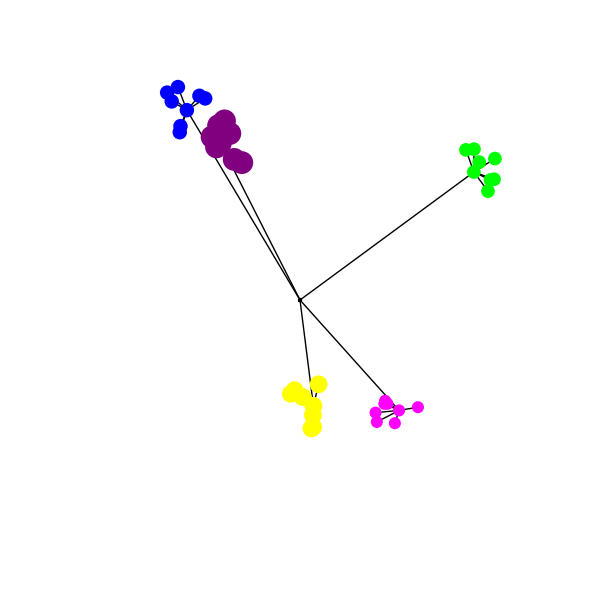

```mathematica
myGraphics=Graphics[{linesGtoF,pointsGF,linesFirstFtoAE,pointsOfAEcoordinatesOfFirstF,linesSecondFtoAE,pointsOfAEcoordinatesOfSecondF,linesThirdFtoAE,pointsOfAEcoordinatesOfThirdF,linesFourthFtoAE,pointsOfAEcoordinatesOfFourthF,linesFifthFtoAE,pointsOfAEcoordinatesOfFifthF},PlotRange->{{-10,10},{-10,10}},GridLines->Automatic,ImageSize->imageSizeValue]
```

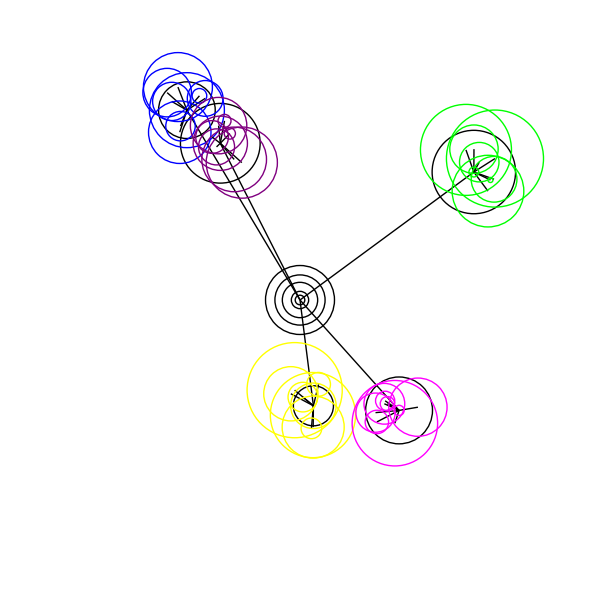

```mathematica
myGraphics/.Point[list_]:>(Circle[#,2*First[Abs[randomCoordinateFunction2]]]&/@list)
```

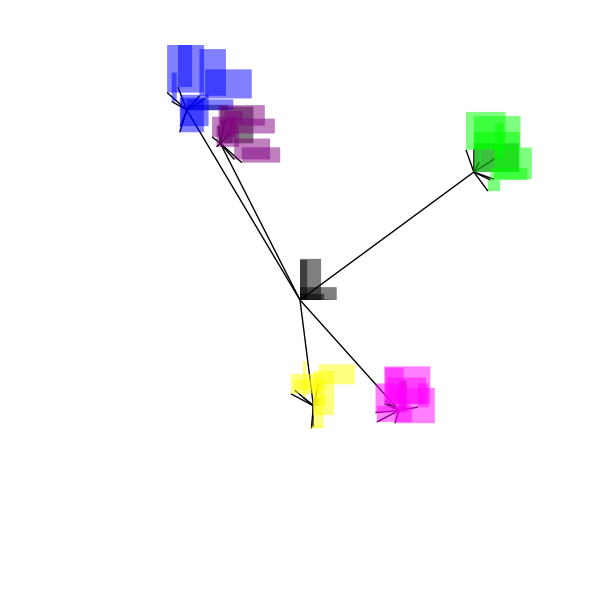

```mathematica
myGraphics/.Point[list_]:>({Opacity[0.5],Rectangle[#,#+2*Abs[randomCoordinateFunction2]]}&/@list)
```

To be continued...

Temporary conclusions:

- As you can see on the latest image, I only implemented level G, F and A or E
- The last level still needs to be written (try to do it)
- The code is redundant and rather dirty :)
- A better way to write would be to define very clean functions, as elegant as possible, and then make use of replacement rules many different structures you would generate thanks to many substitution scenarios 
- You can produce the same result by starting not from G, but from B, C, D or H.
- You should try to implement this version !

Do not forget that you can resize the graphics just by clicking on them and move the frame handle with the mouse
You can also export them. Select them, do a right click, and choose the export options (PDF is good as it keeps the vector lines for edition in Illustrator or rhino etc.)

For the moment the idea is that you learn what is in this notebook, use it to make your project move forward, etc.
Produce scenarios, the code is NEVER a problem (unless you do theoretical computer science...)